Discrete Structures

Relations and Functions

### Overview

Often, it is useful to associate elements of a set to another set.

This association is called a relation; more formally, any subset of a Cartesian product.

Elements of a set can be associated to the same set.

You will also learn about a special class of relation called a function.

-Graphics-

### Graphing

Relations can be visualized as the links between the input set and the output set.

This visualization is a bipartite graph, covered in Lesson 23.

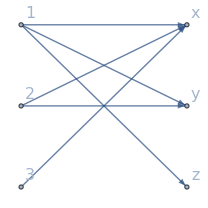

### Functions

A relation R⊆A×B (a∈A,b∈B) is called many-to-one iff (⇔) each value a has a unique b, f(a)=b.

A function is defined as a many-to-one relation.

Is this a valid function?

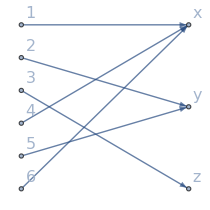

Is this a valid function?

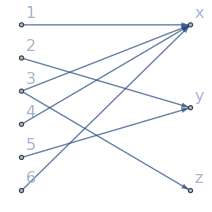

### Examples

Is this a valid function?

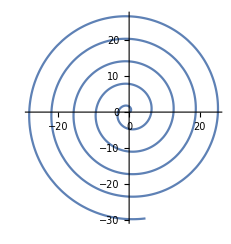

Is this a valid function?

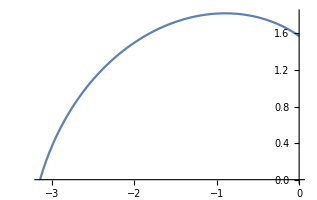

### Domain and Range

Consider a function f(x) from A to B.

Then, the domain (preimage) is the set of values A for which f(x) is defined:

```mathematica
FunctionDomain[Tan[x],x]
```

1/2+x/π∉ℤ

```mathematica
FunctionDomain[Prime[x],x]
```

x∈ℤ&&x≥1

The range (image, codomain) is the set of values B for any f(x) where x∈A:

```mathematica
FunctionRange[Floor[x],x,y]
```

y∈ℤ

```mathematica
FunctionRange[Sin[x],x,y]
```

-1≤y≤1

#### Injunction

For arbitrary m,n, a function f(x) is injective (one-to-one) iff f(x_1)≠f(x_2) when x_1≠x_2.

For domain {1,2,3,4} and range {v,w,x,y,z}, the following function is injective.

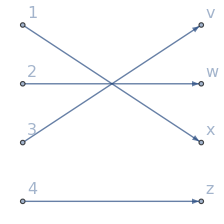

#### Surjection

A function f(x)⊆A×B (a∈A,b∈B) is called surjective (onto) iff each value b has at least one value a, f(a)=b.

For domain {1,2,3,4,5,6} and range {x,y,z}, the following function is surjective.

### Invertibility

A function f is bijective (one-to-one correspondence) iff it is both injective and surjective.

A bijective function is invertible. For the invertible function f(x), the inverse function is denoted f^-1(x).

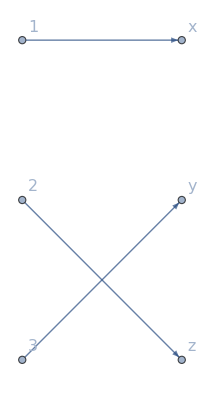
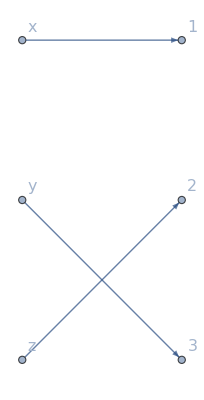
```mathematica
-Graphics-    ->    -Graphics-
```

```mathematica
InverseFunction[Log]
```

Exp

### Examples

Is f(x)=x^2 invertible?



```mathematica
Plot[x^2,{x,-2,2}]
```

```mathematica
FunctionBijective[x^2,x]
```

False

Is f(x)=x^3 invertible?

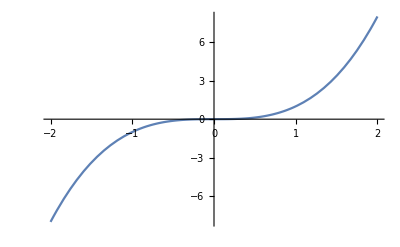

```mathematica
Plot[x^3,{x,-2,2}]
```

```mathematica
FunctionBijective[x^3,x]
```

True

### Composition

The nesting of two or more functions to form a single new function is known as composition.

f(g(x)) or (f∘g)(x) in mathematics

```mathematica
f[g[x]]or f@g@x (*in code*)
```

This is a core principle of Wolfram Language, as well as many other functional programming languages.

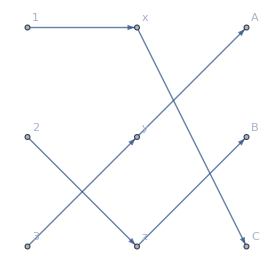

### Example

Consider the functions f(x)=-x/(-1+x) and g(x)=Log(x):

Find the domain and range of (f^-1∘g^-1) (x):

```mathematica
h[x_]:=InverseFunction[-#/(-1+#)&][InverseFunction[Log][x]]
```

```mathematica
FunctionDomain[h[x],x]
```

True

```mathematica
FunctionRange[h[x],x,y]
```

0<y<1

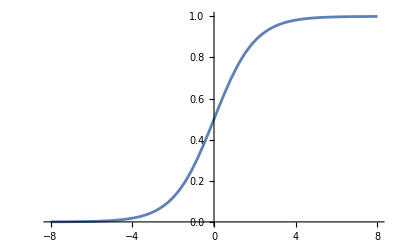

```mathematica
Plot[h[x],{x,- 8,8}]
```

```mathematica
h[x]
```

ⅇ^x/(1+ⅇ^x)

### Summary

From the Cartesian products of set theory, relations can be made.

Many-to-one relations are called functions; bijective functions are called invertible functions.

Composition is a core mechanic of functional programming.

Writing every single binary operator in a large function can easily get tedious.

The next lesson introduces larger operations to make functions more powerful.

Download Notebook »